```mathematica
ClearAll
```

ClearAll

```mathematica
Tensors = {6,8,9,11,12,15,16,19,20,24};
```

## Tensor Definitions

```mathematica
(*Remove["Global`*"]*)
```

Mathematica build-in function like ‘Symmetrize[]’ and ‘TensorContract[]’ seem 
to work really slow or fail due to memory requirements on fully symmetric tensors 
with degree >10.
We define our own functions below based on a simply array data structure for fully symmetric tensors.

```mathematica
Clear[n,degree,idx,idx1,A,b,id3,IDX]
Unprotect[TensorDegree];

(*Every symmetric tensor can be identified with the help of a 2D array say a[N][3] where N is the total number of indepedent variables it has. So every row ie a[i] store the number of entries for x in a[i][1],for y in a[i][2] and for z in a[i][3]*)
IDXFull[n_]:=Flatten[Table[Table[{n-ii,ii-jj,jj},{jj,0,ii}],{ii,0,n}],1]

(*does the same thing as IDXFull but for trace free tensors*)
IDXtrfFull[n_]:=Flatten[Table[Table[{n-ii,ii-jj,jj},{jj,0,Min[ii,1]}],{ii,0,n}],1]

Do[
IDX[degree]=IDXFull[degree];
IDXtrf[degree]=IDXtrfFull[degree];
,{degree,0,40}]

(*given an array list, the following function counts the number of 1s, 2s and 3s*)
toIDX1[list_]:=Map[Count[list,#]&,{1,2,3}] (* Input cartesean indices, e.g. {1,1,2,1,3} *)

(*the Total of the list is the tensorial degree we are interested in. So list should be a 3X1 array and the following function will give us the n corresponding to which a[n] = list.*)
toIDX2[list_]:=Position[IDX[Total[list]],list]⟦1,1⟧ (* Input triple of #indices in {1,2,3} *)
(*same as above but for trace free tensors*)
toIDX3[list_]:=Position[IDXtrfFull[Total[list]],list]⟦1,1⟧ (* Input triple of #indices in {1,2,3} *)

(*Gives the tensor degree of a symmetric tensor.
CAUTION: the formulae is not valid for trace free tensors.*)
TensorDegree[A_]:=1/2 (-3+√(1+8 Length[A]))

id3={{1,0,0},{0,1,0},{0,0,1}};

DeltaValues[list_]:=Block[{a=list⟦1⟧,b=list⟦2⟧,c=list⟦3⟧},
If[OddQ[a]||OddQ[b]||OddQ[c],0,Multinomial[a/2,b/2,c/2]/Multinomial[a,b,c]]
];

(*applied deltavalues to all the components of an even degree tensor*)
DeltaTensor2[degree_?EvenQ]:=Map[DeltaValues,IDX[degree]];

(*What does this do?*)
SymTrace2[A_]:=Block[{dim=3,idx,idx1,degree=TensorDegree[A],length,res},
length=Length[IDX[degree-2]];
res=ConstantArray[0,length];
Do[
res⟦jj⟧=Expand[Sum[A⟦toIDX2[IDX[degree-2]⟦jj⟧+2 id3⟦ii⟧]⟧,{ii,1,dim}]];
,{jj,1,length}];

res
];

SymTraces[A_,n_]:=Module[{res=A},
Do[res=SymTrace2[res],{ii,1,n}];
res
];

(*if the format of the input is IDX, then the output is also in IDX,
Assumes 3 dimensions. And so *)
(* contraction of a symmetric tensor A with Subscript[b, i] *)
SymDot2[A_,b_?VectorQ]:=Block[{dim=3,idx,idx1,degree=TensorDegree[A],length,res},
length=Length[IDX[degree-1]];
res=ConstantArray[0,length];
Do[
(*Lets take a particular term say Ai1i2..xbx. In the result only those components will appear in which x atleast appears once and that's why the addition of id3[[iis]]*)
res⟦jj⟧=Expand[Sum[A⟦toIDX2[IDX[degree-1]⟦jj⟧+id3⟦ii⟧]⟧b⟦ii⟧,{ii,1,dim}]];
,{jj,1,length}];

res
];

(*if the format of the input is IDX, then the output is also in IDX*)
(* full contraction of two symmetric tensors A, B with same degree *)
SymFullDot[A_,B_]:=Block[{dim=3,idx,idx1,degree=TensorDegree[A],length,res},
If[TensorDegree[B]≠degree,Return[0]];
length=Length[IDX[degree]];
res=0;
Do[
idx=IDX[degree]⟦jj⟧;
res+=Multinomial[idx⟦1⟧,idx⟦2⟧,idx⟦3⟧]A⟦jj⟧B⟦jj⟧;
,{jj,1,length}];

res
];

(* symmetric tensor product of a symmetric tensor A with Subscript[b, i] *)
SymProduct2[A_,b_?VectorQ]:=Block[{dim=3,idx,idx1,degree=TensorDegree[A],length,res},
If[degree==0,Return[A⟦1⟧ b]];
length=Length[IDX[degree+1]];
res=ConstantArray[0,length];
Do[
res⟦jj⟧=
1/(degree+1)Sum[
If[(idx=IDX[degree+1]⟦jj⟧)⟦ii⟧>0,idx⟦ii⟧ A⟦toIDX2[idx-id3⟦ii⟧]⟧b⟦ii⟧,0],{ii,1,dim}];
,{jj,1,length}];

res
];

(* symmetric tensor product of a symmetric tensor A with Subscript[δ, ij] *)
SymProductDelta2[A_]:=Block[{dim=3,idx,idx1,degree=TensorDegree[A],length,res},
length=Length[IDX[degree+2]];
res=ConstantArray[0,length];
Do[
res⟦jj⟧=1/((degree+2)(degree+1))Sum[
If[(idx=IDX[degree+2]⟦jj⟧)⟦ii⟧≥2,idx⟦ii⟧(idx⟦ii⟧-1)A⟦toIDX2[idx-2id3⟦ii⟧]⟧,0],{ii,1,dim}];
,{jj,1,length}];

res
];

(*converts a symmetric tensor into a trace free tensor*)
(* returns the tracefree part of a symmetric tensor, but with all components *)
SymTracefree[A_]:=Block[{dim=3,idx,idx1,degree=TensorDegree[A],length,res,trace,res1},
length=Length[IDX[degree]];
res=trace=A;
Do[
res1=trace=SymTrace2[trace];
Do[res1=SymProductDelta2[res1],{ll,1,kk}];
res+=(((-1)^kk degree!)/((degree-2kk)!2^kk kk!)∏_(jj=degree-kk)^(degree-1) 1/(2jj+1))res1;
,{kk,1,degree/2}];

res
];
```

```mathematica
trfEvaluate[A_,list_]:=Module[{a,b,c,m,dim=3,degree=(Length[A]-1)/2,length,res},
{a,b,c}=list;
m=Floor[c/2];
If[c≤1,
res=A⟦toIDX3[list]⟧,
res=(-1)^m Sum[Binomial[m,i]A⟦toIDX3[list+2i id3⟦1⟧+2(m-i) id3⟦2⟧-2m id3⟦3⟧]⟧,{i,0,m}]
];
res
];

(*say we have a trace free tensor, whose independent components are given then the following function will introduce those components in the list which have been negelected due to the trace free nature of the tensor. For eg. it will introduce -Rxx-Ryy for a second order tensor*)
trf2sym[A_]:=Map[Apply[trfEvaluate[A,{#1,#2,#3}]&,#]&,IDX[(Length[A]-1)/2]]

(*Pick the 2D variables from a list containing all the indices.The list will be obtained from the IDXtrf routine. freeindex is the total number of free indices in the tensor*)
Pick2D[freeindex_]:=Pick[IDXtrf[freeindex],Flatten[Join[{1},Table[{1,0},{k,1,freeindex}]]],1];
```

```mathematica
SymTensorForm[A_]:=Block[{degree=TensorDegree[A],length},
length=Length[IDX[degree]];
Table[Apply[{$[#1,#2,#3],A⟦ii⟧}&,IDX[degree]⟦ii⟧],{ii,1,length}]//TableForm
];
```

```mathematica
SymProductDelta2[SymProductDelta2[SymProductDelta2[Map[Apply[A[#1,#2,#3]&,#]&,IDX[1]]]]]
```

{A[1,0,0],1/7 A[0,1,0],1/7 A[0,0,1],1/7 A[1,0,0],0,1/7 A[1,0,0],3/35 A[0,1,0],1/35 A[0,0,1],1/35 A[0,1,0],3/35 A[0,0,1],3/35 A[1,0,0],0,1/35 A[1,0,0],0,3/35 A[1,0,0],1/7 A[0,1,0],1/35 A[0,0,1],1/35 A[0,1,0],1/35 A[0,0,1],1/35 A[0,1,0],1/7 A[0,0,1],1/7 A[1,0,0],0,1/35 A[1,0,0],0,1/35 A[1,0,0],0,1/7 A[1,0,0],A[0,1,0],1/7 A[0,0,1],1/7 A[0,1,0],3/35 A[0,0,1],3/35 A[0,1,0],1/7 A[0,0,1],1/7 A[0,1,0],A[0,0,1]}

```mathematica
Expand[SymTracefree[Map[Apply[A[#1,#2,#3]&,#]&,IDX[2]]]]
```

{-1/3 A[0,0,2]-1/3 A[0,2,0]+2/3 A[2,0,0],A[1,1,0],A[1,0,1],-1/3 A[0,0,2]+2/3 A[0,2,0]-1/3 A[2,0,0],A[0,1,1],2/3 A[0,0,2]-1/3 A[0,2,0]-1/3 A[2,0,0]}

```mathematica
Expand[SymTracefree[Map[Apply[#1+2.#2-3#3&,#]&,IDX[4]]]]
```

{-1.14286,1.14286,2.57143,3.42857,1.42857,-2.28571,3.14286,2.85714,-4.28571,-5.42857,-2.28571,4.28571,-1.14286,-5.71429,3.42857}

```mathematica
Expand[SymFullDot[SymTracefree[trf2sym[{Rxx,Rxy,0,Ryy,0}]],SymTracefree[trf2sym[{Sxx,Sxy,0,Syy,0}]]]]
```

2 Rxx Sxx+Ryy Sxx+2 Rxy Sxy+Rxx Syy+2 Ryy Syy

```mathematica
Normal[CoefficientArrays[Normal[CoefficientArrays[Expand[SymFullDot[SymTracefree[trf2sym[{Rxx,Rxy,0,Ryy,0}]],SymTracefree[trf2sym[{Sxx,Sxy,0,Syy,0}]]]],{Rxx,Rxy,Ryy}]]⟦2⟧,{Sxx,Sxy,Syy}]⟦2⟧]
```

{{2,0,1},{0,2,0},{1,0,2}}

```mathematica
Normal[CoefficientArrays[Normal[CoefficientArrays[Expand[SymFullDot[SymTracefree[trf2sym[{mxxx,mxxy,0,mxyy,0,myyy,0}]],SymTracefree[trf2sym[{nxxx,nxxy,0,nxyy,0,nyyy,0}]]]],{mxxx,mxxy,mxyy,myyy}]]⟦2⟧,{nxxx,nxxy,nxyy,nyyy}]⟦2⟧]
```

{{4,0,3,0},{0,6,0,3},{3,0,6,0},{0,3,0,4}}

## Basic Definitions

```mathematica
(*ref to manuels paper on fluxes for large moment system for a detailed expression*)
(*total tensorial degree including traces*)
iFullDegree[i_]=Floor[√(4i-3)-1];
(*number of traces C^2 has one trace*)
iTraces[i_]=Floor[(1+1/2 iFullDegree[i])^2]-i;
(*actual tensorial degree*)
iTensorDegree[i_]=iFullDegree[i]-2iTraces[i];
ii[s_,A_]=Floor[(A+2(s+1))/2](A+2(s+1)-Floor[(A+2(s+1))/2])-s;

(*i is as defined in the reference*)
NumberOfVariables2D[ntensors_]:=Sum[iTensorDegree[i]+1,{i,1,ntensors}];
NumberOfVariables3D[ntensors_]:=Sum[2iTensorDegree[i]+1,{i,1,ntensors}];
NumberOfFullTensors3D[ntensors_]:=Block[{m=iFullDegree[ntensors],frac},
m-(((m+1)(m+2)(m+3))/6.-Sum[2iTensorDegree[i]+1,{i,1,ntensors}])/(((m+1)(m+2))/2)
];

varName[s_,ix_,iy_,iz_]:=StringJoin["ρ",ToString[s],ConstantArray["x",ix],ConstantArray["y",iy],ConstantArray["z",iz]]


(*this is not the norm of ψ, rather it's the norm of the laguerre polynomials*)
Normψ[a_,deg_]=(deg!a!Gamma[deg+a+3/2])/Gamma[deg+3/2];

(*given a tensor W extract all the independed components in 2D in case of trace free situation*)
trfComponents2D[W_]:=Extract[W,Map[Position[IDX[TensorDegree[W]],#]⟦1⟧&,Pick[IDXtrf[TensorDegree[W]],Flatten[Join[{1},Table[{1,0},{k,1,TensorDegree[W]}]]],1]]]


trfVar2D[deg_,name_]:=Table[name[i],{i,1,deg+1}]
From2Dto3D[list_]:=Flatten[Join[{list⟦1⟧},Table[{list⟦k⟧,0},{k,2,Length[list]}]]]


R2[0,1]={{1},{0}};
R2[0,2]={{0},{1}};

Do[
(*Given the components of a tensor represented by B, then tmp collects the terms corresponding to \partial_x in \partial_<x_{in} w_{i1..in>}
the second one does the same job but for a tensor product. *)
tmp=Normal[CoefficientArrays[trfComponents2D[SymDot2[trf2sym[From2Dto3D[trfVar2D[d,B]]],{dx,dy,0}]],{dx,dy}]]⟦2⟧;
(*store the coefficient infront of the moments*)
Do[R1[d,i]=CoefficientArrays[tmp⟦All,i⟧,trfVar2D[d,B]]⟦2⟧,{i,1,2}];

(*same as above but for tensor products*)
tmp=Normal[CoefficientArrays[trfComponents2D[SymTracefree[SymProduct2[trf2sym[From2Dto3D[trfVar2D[d,B]]],{dx,dy,0}]]],{dx,dy}]]⟦2⟧;
(*store the coefficients infront of the moments*)
Do[R2[d,i]=CoefficientArrays[tmp⟦All,i⟧,trfVar2D[d,B]]⟦2⟧,{i,1,2}];
,{d,1,15}];

(*The following is the main moment equation*)
recursion1[a_,deg_,flag_]:=(
√((2 deg+2)/(2deg+3))(√(deg+a+3/2)R1[deg+1,flag].trfVar2D[deg+1,ψ[#,a,deg+1]&]-√a R1[deg+1,flag].trfVar2D[deg+1,ψ[#,a-1,deg+1]&])
+If[deg>0,√((2deg)/(2deg+1))(√(deg+a+1/2)R2[deg-1,flag].trfVar2D[deg-1,ψ[#,a,deg-1]&]-√(a+1)R2[deg-1,flag].trfVar2D[deg-1,ψ[#,a+1,deg-1]&]),0])

(*(Give two Laguerre polynomials Subscript[(L^(n)), a] and Subscript[(L^(m)), b] then the following routine computes (∫^∞)_0 Subscript[(L^(n)(x^2/2)), a](L^(m)(x^2/2))))_b x^2 ⅇ^(-x^2/2)dx. Uses the Laguerre polynomials used in file CompleteGenericMatrices1D.nb*)
mixed[a_,n_,b_,m_]:=Expand[Sum[Binomial[n-(n+m)/2+a-c1-1,a-c1](a!)/(c1!)Binomial[m-(n+m)/2+b-c1-1,b-c1](b!)/(c1!)(c1!√2 Gamma[(n+m)/2+c1+3/2] 2^((n+m)/2)),{c1,0,Min[a,b]}]];

(*ratio between the new and old laguerre polynomials*)
factorLaguerre[a_,n_]:=√(Gamma[n+3/2]/(n!a!Gamma[n+a+3/2]));

(*Same as above but for Laguerre polynomials used in the Boundary Value problem paper*)
mixed2[a_,n_,b_,m_]:=Expand[mixed[a,n,b,m]factorLaguerre[a,n]factorLaguerre[b,m]];

(*The following function integrates expressions of the kind ∫νx^m νy^p νz^n dν but the integration is such that only νx >0. Making the transformation to spherical coordinates i.e. νx = Sin ν Cos θ, νy = Sin ν Sin θ and νz = Cos ν we have (∫^(+π/2))_(-π/2)(∫_0)^π(Sinν^(mm+nn+1)Cosν^pp Sinθ^nn Cosθ^mm)dνdθ*)

IntegrateHalfNxNyNz1[ex_]:=Block[{pos1,pos2,pos3,mm=0,nn=0,pp=0,res,res1=νx νy νz ex},
pos1=Position[res1,νx^_];
pos2=Position[res1,νy^_];
pos3=Position[res1,νz^_];
If[Length[pos1]>0,mm=Extract[res1,pos1⟦1⟧]⟦2⟧-1];
If[Length[pos2]>0,nn=Extract[res1,pos2⟦1⟧]⟦2⟧-1];
If[Length[pos3]>0,pp=Extract[res1,pos3⟦1⟧]⟦2⟧-1];
res=Delete[res1,Join[pos1,pos2,pos3]]If[OddQ[nn]||OddQ[pp],0,2π((nn-1)!!(mm-1)!!(pp-1)!!)/((nn+mm+pp+1)!!)];
If[Length[pos1]==0,res=res/νx];
If[Length[pos2]==0,res=res/νy];
If[Length[pos3]==0,res=res/νz];
res
]

(*applies integrate halfnxnynz1 to a long expression*)
IntegrateHalfNxNyNz[ex_]:=If[Head[ex]=== Plus,
Apply[Plus,Table[IntegrateHalfNxNyNz1[ex⟦ii⟧],{ii,1,Length[ex]}]],
IntegrateHalfNxNyNz1[ex]]


(*The input of the following function i.e idx1 and idx2 are arrays such that idx1[[{2,3,4}]] = {#xcomponents,#ycomponents,#zcomponents}. The following function computes the half integrals of the form ∫ ψ fdc where ψ is the basis function and the integral is only over the half space. The ψ is represented by one of the input parameters and the basis functions in f are represented by one of the input parameters.

idx1 = index for the testfunction
	   ix2 = index for the basis of the distribution function*)

HalfIntegrate[idx1_,idx2_]:=Block[{Int1,Int2,deg1=Total[idx1⟦{2,3,4}⟧],deg2=Total[idx2⟦{2,3,4}⟧],f0},

(*The following term develops terms of the form ν_(<x^m y^n>). The algorithm is as follows
1. Extract the total number of free indices in the tensor
2. Develop the full sym trace free tensor i.e develop all the components of ν_(<i_(1...)Subscript[i, n]>)
3. Extract the component corresponding to idx1*)

Int1=Expand[SymTracefree[Map[Apply[νx^#1 νy^#2 νz^#3&,#]&,IDX[deg1]]]⟦toIDX2[idx1⟦{2,3,4}⟧]⟧];

(*Let us consider the part of the distribution function which comes from Rij. This part will be of the form Rxx...+Rzz.... But Rzz = -Rxx-Ryy and therefore Int2 is not simply the tensorised ν_(<x^m y^n>)*)
Int2=SymFullDot[Map[Apply[νx^#1 νy^#2 νz^#3&,#]&,IDX[deg2]],trf2sym[Map[Apply[If[{#1,#2,#3}==idx2⟦{2,3,4}⟧,1,0]&,#]&,IDXtrf[deg2]]]];
f0= 1/(2 π)^(3/2);

Expand[mixed2[idx1⟦1⟧,deg1,idx2⟦1⟧,deg2]f0 IntegrateHalfNxNyNz[Expand[Int1 Int2]]]
]
```

## System Matrices

### Boundary Matrix

```mathematica
(*same as below but without normal relaxational velocity*)
DevelopBNoRelax[BC_,var_]:=Module[{result,eqnVelocity,tempBC,eqnρW,transformρW,g,IdxVelocity},

(*put the normal velocity to zero. Assumption is that the wall is at rest.*)
tempBC =Flatten[Expand[√π BC]/.{w[0,1,0,0]->0}];
eqnρW = tempBC⟦1⟧;
transformρW = Solve[eqnρW==0,{Subscript[w, wall][0,0,0,0]}];
tempBC = Flatten[Expand[tempBC/.transformρW]];

{g,result} = CoefficientArrays[tempBC,var];

(*put the velocity index to zero*)
IdxVelocity=2;
result⟦1,IdxVelocity⟧=1;

{g,result}
]
```

### Check Null Space Variables

```mathematica
CheckNullSpaceVariables[var_,MaxDegree_]:=Module[{result},

numOdd =Map[If[OddQ[#⟦2⟧],#]&,var];
]
```

### System Matrices

```mathematica
GetMatricesHeatConduction[Ntensors_]:=Block[{varIdx,varIdxComplete,var,Ax,
varOdd,varIdxCompleteEven,varEven,BCrhs,varIdxCompleteOdd,IntGasEven,IntGasOdd,varIdxWall,IntWall,B,varIdxCompleteHeat,locateHeatVar,varIdxCompleteTrun,locateOddHeatVar,MaxDegree},

varIdx=Table[{iTraces[i],iTensorDegree[i]},{i,1,Ntensors}];
MaxDegree = Max[Flatten[Map[2*#⟦1⟧+#⟦2⟧&,varIdx]]];

varIdxComplete=Flatten[Table[Map[Join[{varIdx⟦n,1⟧},#]&,Pick[IDXtrf[varIdx⟦n,2⟧],Flatten[Join[{1},Table[{1,0},{k,1,varIdx⟦n,2⟧}]]],1]],{n,1,Length[varIdx]}],1];

var=Table[Apply[Function[{a,deg},trfVar2D[deg,ψ[#,a,deg]&]],item],{item,varIdx}];

Ax=CoefficientArrays[Flatten[Table[Apply[Function[{a,deg},recursion1[a,deg,1]],item],{item,varIdx}]],Flatten[var]]⟦2⟧;



(*Picks out the even components. The fourth component is anyhow always zero.*)
varIdxCompleteEven=Select[varIdxComplete,(EvenQ[#⟦2⟧]&&#⟦4⟧==0)&];

(*Picks out the odd variables*)
varIdxCompleteOdd=Select[varIdxComplete,(OddQ[#⟦2⟧]&&#⟦4⟧==0)&];

varOdd=Flatten[Position[varIdxComplete,Alternatives@@varIdxCompleteOdd]];
varIdxWall = {{0,0,0,0},{1,0,0,0}};

IntGasEven=Table[
If[OddQ[idx⟦2⟧],
Total[Map[HalfIntegrate[idx,#]Apply[w,#]&,Table[idx2,{idx2,varIdxCompleteEven}]]]
,0]
,{idx,varIdxCompleteOdd}];

IntGasOdd=Table[
If[OddQ[idx⟦2⟧],
Total[Map[HalfIntegrate[idx,#]Apply[w,#]&,Table[idx2,{idx2,varIdxCompleteOdd}]]]
,0]
,{idx,varIdxCompleteOdd}];

IntWall = Table[
If[OddQ[idx⟦2⟧],
Total[Map[HalfIntegrate[idx,#]Apply[Subscript[w, wall],#]&,Table[idx2,{idx2,varIdxWall}]]]
,0]
,{idx,varIdxCompleteOdd}];

B = DevelopBNoRelax[Expand[IntGasOdd-IntGasEven+IntWall],Map[Apply[w,#]&,varIdxComplete]]⟦2⟧;

(*Manupilations for heat conduction*)

varIdxCompleteHeat=Map[If[#⟦3⟧==0,#,{}]&,varIdxComplete];

varIdxCompleteHeat = Select[varIdxCompleteHeat,UnsameQ[#,{}]&];

(*Remove the bad Ones. If even and not of max degree then keep. If odd, always keep*)
varIdxCompleteHeat=Map[If[EvenQ[#⟦2⟧],If[2#⟦1⟧+Total[#⟦2;;-1⟧]≠MaxDegree,#,{}],#]&,varIdxCompleteHeat];

varIdxCompleteHeat = Select[varIdxCompleteHeat,UnsameQ[#,{}]&];

locateHeatVar = Flatten[Position[varIdxComplete,Alternatives@@varIdxCompleteHeat]];

(*oods in which the y does not appear*)
locateOddHeatVar = Map[If[#⟦3⟧==0,#]&,varIdxCompleteOdd];

locateOddHeatVar = Flatten[Position[varIdxCompleteOdd,Alternatives@@locateOddHeatVar]];

(*removing the variables which are not needed and also rho and velocity*)
Ax=Ax⟦locateHeatVar,locateHeatVar⟧⟦3;;-1,3;;-1⟧;
B = B⟦locateOddHeatVar,locateHeatVar⟧⟦2;;-1,3;;-1⟧;

(*when the wall normal points out of the gas.*)
{Ax,B.(Map[Apply[w,#]&,varIdxComplete⟦locateHeatVar⟧]⟦3;;-1⟧)}

];
```

# Solving Heat Conduction

## Return the Heat Conduction Variables

```mathematica
(*Given full set of variables, the following routine returns the variables involved in heat conduction.
These are those variables which have only an x-index. Since they are the ones which are involved in the heat conduction.*)
ReturnHeatVar[var_]:=Module[{result,pos},
result={};
pos={};

(*The assumption is that none of the variables contain the z-index. Therefore we only check for the y index. If the y index is zero then the variabls is involved in heat conduction*)
Do[If[var⟦ii⟧⟦3⟧==0,result=Join[result,{var⟦ii⟧}];pos=Join[pos,{{ii}}];];
,{ii,1,Length[var]}];

(*we also return the total number of variables involved in the heat conduction. The final result includes at first the variables involved in heat conduction and then the variables which were left out.*)
{Join[result,Delete[var,pos]],Length[pos]}
]
```

## Return the Matrix for Heat Conduction

```mathematica
MatrixHeat[Mat_,var_,varHeat_,numHeat_]:=Module[{Permute,PermuteInv,MatHeat},

Permute=PermuteVar[var,varHeat];
PermuteInv=PermuteVar[varHeat,var];

MatHeat=PermuteInv.Mat.Permute;

(*we first extract the matrix which plays a role in heat conduction*)
MatHeat=MatHeat⟦1;;numHeat,1;;numHeat⟧;

(*we now remove the rows corresponding to normal velocity and density. That means the upper block of 2 X 2 size*)
MatHeat=MatHeat⟦3;;-1,3;;-1⟧;

MatHeat
]
```

## Solving Routine(Core)

```mathematica
Clear[res,nn,var,eqn,B0,A0,P0,a,n,w,ww,unknowns,λ0,λ,λPlus,vv,v,Ansatz,Coefs,v0,v1,v2,v3,v4,C0,k,x,α,u]
GetSolutionHeat[Ntensors_,flag_,type_]:=Block[{res,nn,var,varC,eqn,b0,a,n,w,dw,λ0,λ,λPlus,v,vv,Ansatz,Coefs,C0,Signum,SymmetryConditions,k,x,jj,ii,Kn,α,numEqn,coef},

(*Delete is for removing the density and the velocity. The reason for removing the first equation is obvious. aIdx[[1]]+1 removes the energy balance because it contains the denstiy and the stress tensor. Since we are not interested in density, we let it go.*)


SystemData=TruncateMat[Ntensors,flag];
A0=MatrixHeat[SystemData⟦1⟧,SystemData⟦3⟧,ReturnHeatVar[SystemData⟦3⟧]⟦1⟧,ReturnHeatVar[SystemData⟦3⟧]⟦2⟧];
numEqn=Length[A0];

P0=SparseArray[{{i_,i_}->-1},numEqn];

(*only for energy balance, the momentum equation and the mass conservation has been ignored. *)
P0⟦1,1⟧=0;

(*generalized eigen vector and eigen value of P0 with respect to A0*)
{λ0,vv}=Chop[Eigensystem[{P0,1.0A0}]];

(*remove the zero and the infinite eigen values, why do the infinite eigen values appear? *)
λ=Select[λ0,(0<Abs[#]<∞)&];
v=Extract[vv,Flatten[Table[Position[λ0,item],{item,Select[λ0,(0<Abs[#]<∞)&]}],1]];

(*assumes symmetric spectrum and a certain ordering of the EV. First we have the negative ones and then the positive ones*)
λ=Flatten[Table[{Rationalize[λ⟦ii⟧,0],-Rationalize[λ⟦ii⟧,0]},{ii,1,Length[λ],2}]];

λPlus=Select[λ,(#>0)&];

If[type == 1,coef[0,3]=Kn k[0]];

(*a polynomial ansatz for homogeneous solution*)
Ansatz[x_]=Table[Sum[coef[jj,ii] x^jj,{jj,0,4}],{ii,1,numEqn}];
Coefs=Cases[Flatten[Table[Table[coef[jj,ii],{jj,0,4}],{ii,1,numEqn}]],coef[_,_]];

(*vector for the forcing term*)
B0=Table[0,{i,1,numEqn}];

(*only for poisson heat conduction we have the forcing*)
If[type==0,B0⟦1⟧=1];


(*ansatz for the particular solution of the equations.*)
Ansatz[x_]=Ansatz[x]/.Solve[Thread[Flatten[CoefficientList[A0.Ansatz'[x]-1/Kn P0.Ansatz[x]+α B0 x^2,x]]==0],Coefs]⟦1⟧/.{coef[_,_]->0};

Signum=Table[0,{ii,1,Length[λ],2}];

(*store the sign of the first non-zero entry in the eigenvectors*)

Do[jj=1;While[v⟦ii,jj⟧==0,jj++];Signum⟦(ii+1)/2⟧=-Sign[v⟦ii+1,jj⟧/v⟦ii,jj⟧],{ii,1,Length[λ],2}];

If[type==0,SymmetryConditions=Table[k[ii]->-Signum⟦(ii+1)/2⟧k[ii+1],{ii,1,Length[λ],2}],SymmetryConditions=Table[k[ii]->Signum⟦(ii+1)/2⟧k[ii+1],{ii,1,Length[λ],2}]];

(*The final result is the particular solution + the solution to the homogeneous problem. The particular solution is the Ansatz and the homogeneous solution is the part: C0 B0+Sum[k[ii] v⟦ii⟧Exp[λ⟦ii⟧x/Kn]*)

res=Chop[ExpToTrig[C0 B0+Ansatz[x]+Sum[k[ii] v⟦ii⟧Exp[λ⟦ii⟧x/Kn],{ii,1,Length[λ]}]/.SymmetryConditions/.Table[k[ii]->k[ii/2],{ii,1,Length[λ]}]]]/.Table[k[ii]->k[ii]Exp[-λPlus⟦ii⟧(1/2)/Kn],{ii,1,Length[λPlus]}]


];
```

```mathematica
u[x_]=GetSolutionHeat[11,1,1];

Chop[Expand[N[A0.u'[x]-1/Kn P0.u[x]+α B0 x^2]]]
```

{0,0,0,0,0,0,0,0}

## Boundary Conditions

```mathematica
GetBoundaryHeat[B_,var_,varOdd_]:=Module[{result,PermuteMat,varHeat,Bheat,PermuteMatOdd,varHeatOdd,numVarHeat,numVarHeatOdd,Brhs},


{varHeat,numVarHeat}=ReturnHeatVar[var];
{varHeatOdd,numVarHeatOdd}=ReturnHeatVar[var⟦varOdd⟧];

PermuteMat=PermuteVar[var,varHeat];
PermuteMatOdd=PermuteVar[varHeatOdd,var⟦varOdd⟧];

(*Ignoring the boundary condition from vx and the contribution from ρ and vx. Originally the boundary conditions are of the form Bu = g. Where u contains all the variables. So we first multiply from the left by the permutation matrix so that we collect the odd variables of the heat conduction problem. Then we multiply from the right so that we collect at the variables for the heat conduction problem. *)
Bheat=FullSimplify[PermuteMatOdd.B.PermuteMat]⟦2;;numVarHeatOdd,3;;numVarHeat⟧;
Brhs=-√(3/2)Bheat⟦All,1⟧thetaW;
(*We return the boundary in the form B.u+g*)
Bheat.varHeat⟦3;;numVarHeat⟧-Brhs
]
```

## Solving Procedure

```mathematica
(*flag == 0 for Original system and flag == 1 for TG. type==0 means poisson heat conduction*)
GetHeatConduction[kn_,θw_,alpha_,Ntensors_,flag_,type_]:=Module[{varHeat,numVarHeat,U,BC,BCrhs,BCmatrix,bcSol},

U=GetSolutionHeat[Ntensors,flag,type];

(*we first collect all the variables*)
(*The value of SystemData is prescribed inside the GetSolutionHeat*)
{varHeat,numVarHeat}=ReturnHeatVar[SystemData⟦3⟧];

(*we now remove density and velocity from the set of variables*)
varHeat=varHeat⟦3;;numVarHeat⟧;

BC=GetBoundaryHeat[SystemData⟦2⟧,SystemData⟦3⟧,SystemData⟦4⟧];

If[type == 0,{BCrhs,BCmatrix}=CoefficientArrays[(BC/.Table[varHeat⟦ii⟧->U⟦ii⟧/.{x->1/2},{ii,1,Length[varHeat]}]/.{χ1->1,Kn->kn,α->alpha}),Join[{C0},Table[k[ii],{ii,1,Length[BC]-1}]]];,{BCrhs,BCmatrix}=CoefficientArrays[(BC/.Table[varHeat⟦ii⟧->U⟦ii⟧/.{x->1/2},{ii,1,Length[varHeat]}]/.{χ1->1,Kn->kn,α->alpha}),Table[k[ii],{ii,0,Length[BC]-1}]];];

If[type==0,
bcSol=Thread[Join[{C0},Table[k[ii],{ii,1,Length[BC]-1}]]->Chop[-Inverse[BCmatrix].BCrhs]];,bcSol=Thread[Table[k[ii],{ii,0,Length[BC]-1}]->Chop[-Inverse[BCmatrix].BCrhs]];];


{Expand[U/.bcSol/.thetaW->θw/.α->alpha/.Kn->kn],varHeat}
]
```

```mathematica
{factθ,factσ,factq}={-√(2/3),√2,-√(5/2)};
{IDθ,IDσ,IDq}={1,2,-3};
```

# Reference Solution

### Poisson Heat

```mathematica
exactKn0p1 = Import["refs/Archive/BGKPoiseuilleHeat/Result_BGKreduced_tau0p1_nst600_Nc300_cMax5p0.dat"];

exactKn0p3 = Import["refs/Archive/BGKPoiseuilleHeat/Result_BGKreduced_tau0p3_nst600_Nc300_cMax5p0.dat"];

exactKn0p5 = Import["refs/Archive/BGKPoiseuilleHeat/Result_BGKreduced_tau0p5_nst600_Nc300_cMax5p0.dat"];

(*fix for the wall temperature*)
exactKn0p1⟦All,4⟧+=1;
exactKn0p3⟦All,4⟧+=1;
exactKn0p5⟦All,4⟧+=1;

θExactKn0p1=Interpolation[exactKn0p1⟦All,{1,4}⟧];
σExactKn0p1 = Interpolation[exactKn0p1⟦All,{1,6}⟧];
qExactKn0p1 = Interpolation[exactKn0p1⟦All,{1,7}⟧];

θExactKn0p3=Interpolation[exactKn0p3⟦All,{1,4}⟧];
σExactKn0p3 = Interpolation[exactKn0p3⟦All,{1,6}⟧];
qExactKn0p3 = Interpolation[exactKn0p3⟦All,{1,7}⟧];

θExactKn0p5=Interpolation[exactKn0p5⟦All,{1,4}⟧];
σExactKn0p5 = Interpolation[exactKn0p5⟦All,{1,6}⟧];
qExactKn0p5 = Interpolation[exactKn0p5⟦All,{1,7}⟧];
```

```mathematica
θExactKn0p3[x]
```

InterpolatingFunction[{{-0.5, 0.5}}, <>][x]

### Heat Conduction

```mathematica
exactHCKn0p1 = Import["refs/Archive/BGKSimpleHeat/Result_BGKreduced_tau0p1_nst600_Nc300_cMax5p0.dat"];

exactHCKn0p3 = Import["refs/Archive/BGKSimpleHeat/Result_BGKreduced_tau0p3_nst600_Nc300_cMax5p0.dat"];

exactHCKn0p5 = Import["refs/Archive/BGKSimpleHeat/Result_BGKreduced_tau0p5_nst600_Nc300_cMax5p0.dat"];

(*fix for the wall temperature*)
(*exactHCKn0p1⟦All,4⟧+=1;
exactHCKn0p3⟦All,4⟧+=1;
exactHCKn0p5⟦All,4⟧+=1;*)

θExactHCKn0p1=Interpolation[exactHCKn0p1⟦All,{1,4}⟧];
σExactHCKn0p1 = Interpolation[exactHCKn0p1⟦All,{1,6}⟧];
qExacHCtKn0p1 = Interpolation[exactHCKn0p1⟦All,{1,7}⟧];

θExactHCKn0p3=Interpolation[exactHCKn0p3⟦All,{1,4}⟧];
σExactHCKn0p3 = Interpolation[exactHCKn0p3⟦All,{1,6}⟧];
qExactHCKn0p3 = Interpolation[exactHCKn0p3⟦All,{1,7}⟧];

θExactHCKn0p5=Interpolation[exactHCKn0p5⟦All,{1,4}⟧];
σExactHCKn0p5 = Interpolation[exactHCKn0p5⟦All,{1,6}⟧];
qExactHCKn0p5 = Interpolation[exactHCKn0p5⟦All,{1,7}⟧];
```

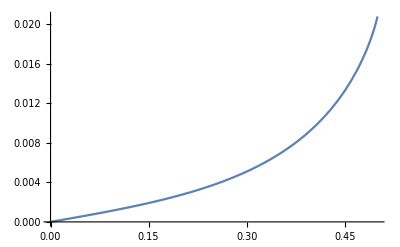

```mathematica
Plot[σExactHCKn0p1[x],{x,0,0.5}]
```

# Results (Poisson Heat Conduction)

### compute L2 error

```mathematica
ComputeL2Norm[data_]:=√2 Sqrt[NIntegrate[(data)^2,{x,0,0.5}]];

ComputeL2Error[Exact_,Num_]:=√2 Sqrt[NIntegrate[(Exact-Num)^2,{x,0,0.5}]];

ComputeErrorEntropy[Exact_,Num_,MomExact_,MomNum_]:=Module[{integrant,entries,varExact,varNum},


(*the difference in the entropy*)
integrant=Total[Flatten[{(Exact⟦1;;Length[Num]⟧-Num)(Exact⟦1;;Length[Num]⟧-Num),(Exact⟦Length[Num]+1;;-1⟧)(Exact⟦Length[Num]+1;;-1⟧)}]];

√2 Sqrt[NIntegrate[integrant,{x,0,0.5}]]];
```

### All theories

#### Kn 0.1

```mathematica
Kn = 0.1;
θW=1.0;
α=√(2/3);
problemType = 0;
systemType = 1;

Do[Print[Style["Num Tensors: ",FontColor->Magenta],ii];
solKn0p1[ii][x_]=GetHeatConduction[Kn,θW,α,ii,systemType,problemType];,{ii,Tensors}];

systemType = 0;
Do[Print[Style["Num Tensors: ",FontColor->Magenta],ii];
solOldKn0p1[ii][x_]=GetHeatConduction[Kn,θW,α,ii,systemType,problemType];,{ii,Tensors}];
```

Num Tensors: 6

Num Tensors: 8

Num Tensors: 9

Num Tensors: 11

Num Tensors: 12

Num Tensors: 15

Num Tensors: 16

Num Tensors: 19

Num Tensors: 20

Num Tensors: 24

Num Tensors: 6

Num Tensors: 8

Num Tensors: 9

Num Tensors: 11

Num Tensors: 12

Num Tensors: 15

Num Tensors: 16

Num Tensors: 19

Num Tensors: 20

Num Tensors: 24

#### Kn 0.3

```mathematica
Kn = 0.3;
θW=1.0;
α=√(2/3);
problemType = 0;
systemType = 1;

Do[Print[Style["Num Tensors: ",FontColor->Magenta],ii];
solKn0p3[ii][x_]=GetHeatConduction[Kn,θW,α,ii,systemType,problemType];,{ii,Tensors}];

systemType = 0;
Do[Print[Style["Num Tensors: ",FontColor->Magenta],ii];
solOldKn0p3[ii][x_]=GetHeatConduction[Kn,θW,α,ii,systemType,problemType];,{ii,Tensors}];
```

Num Tensors: 6

Num Tensors: 8

Num Tensors: 9

Num Tensors: 11

Num Tensors: 12

Num Tensors: 15

Num Tensors: 16

Num Tensors: 19

Num Tensors: 20

Num Tensors: 24

Num Tensors: 6

Num Tensors: 8

Num Tensors: 9

Num Tensors: 11

Num Tensors: 12

Num Tensors: 15

Num Tensors: 16

Num Tensors: 19

Num Tensors: 20

Num Tensors: 24

#### Kn 0.5

```mathematica
Kn = 0.5;
θW=1.0;
α=√(2/3);
problemType = 0;
systemType = 1;

Do[Print[Style["Num Tensors: ",FontColor->Magenta],ii];
solKn0p5[ii][x_]=GetHeatConduction[Kn,θW,α,ii,systemType,problemType];,{ii,Tensors}];

systemType = 0;
Do[Print[Style["Num Tensors: ",FontColor->Magenta],ii];
solOldKn0p5[ii][x_]=GetHeatConduction[Kn,θW,α,ii,systemType,problemType];,{ii,Tensors}];
```

Num Tensors: 6

Num Tensors: 8

Num Tensors: 9

Num Tensors: 11

Num Tensors: 12

Num Tensors: 15

Num Tensors: 16

Num Tensors: 19

Num Tensors: 20

Num Tensors: 24

Num Tensors: 6

Num Tensors: 8

Num Tensors: 9

Num Tensors: 11

Num Tensors: 12

Num Tensors: 15

Num Tensors: 16

Num Tensors: 19

Num Tensors: 20

Num Tensors: 24

#### Kn 1.5

```mathematica
Kn = 1.5;
θW=1.0;
α=√(2/3);
problemType = 0;
systemType = 1;

Do[Print[Style["Num Tensors: ",FontColor->Magenta],ii];
solKn1p5[ii][x_]=GetHeatConduction[Kn,θW,α,ii,systemType,problemType];,{ii,Tensors}];

systemType = 0;
Do[Print[Style["Num Tensors: ",FontColor->Magenta],ii];
solOldKn1p5[ii][x_]=GetHeatConduction[Kn,θW,α,ii,systemType,problemType];,{ii,Tensors}];
```

Num Tensors: 6

Num Tensors: 8

Num Tensors: 9

Num Tensors: 11

Num Tensors: 12

Num Tensors: 15

Num Tensors: 16

Num Tensors: 19

Num Tensors: 6

Num Tensors: 8

Num Tensors: 9

Num Tensors: 11

Num Tensors: 12

Num Tensors: 15

Num Tensors: 16

Num Tensors: 19

#### error computation (Converge macroscopic quantities)

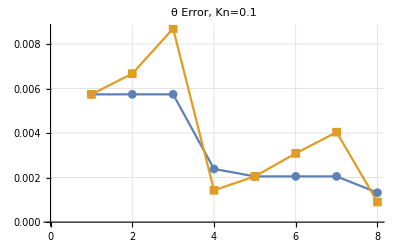

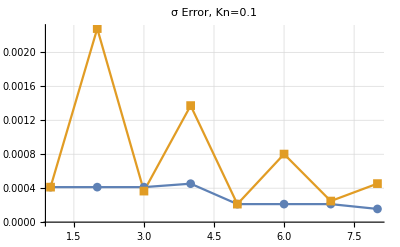

```mathematica
{errorTempKn0p1,errorStressKn0p1} = {Table[ComputeL2Error[θExactKn0p1[x],solKn0p1[ii][x]⟦IDθ⟧*factθ],{ii,Tensors}],Table[ComputeL2Error[σExactKn0p1[x],solKn0p1[ii][x]⟦IDσ⟧*factσ],{ii,Tensors}]};

{errorTempOldKn0p1,errorStressOldKn0p1} = {Table[ComputeL2Error[θExactKn0p1[x],solOldKn0p1[ii][x]⟦IDθ⟧*factθ],{ii,Tensors}],Table[ComputeL2Error[σExactKn0p1[x],solOldKn0p1[ii][x]⟦IDσ⟧*factσ],{ii,Tensors}]};


ListPlot[{errorTempKn0p1,errorTempOldKn0p1},Joined->True,GridLines->Automatic,PlotLabel->"θ Error, Kn=0.1",PlotMarkers->Automatic]


ListPlot[{errorStressKn0p1,errorStressOldKn0p1},Joined->True,GridLines->Automatic,PlotLabel->"σ Error, Kn=0.1",PlotMarkers->Automatic,PlotRange->Full]
```

```mathematica
{errorTempKn0p3,errorStressKn0p3} = {Table[ComputeL2Error[θExactKn0p3,temperatureKn0p3[ii]],{ii,Tensors}],Table[ComputeL2Error[σExactKn0p3,stressKn0p3[ii]],{ii,Tensors}]};
```

```mathematica
{errorTempOldKn0p3,errorStressOldKn0p3} = {Table[ComputeL2Error[θExactKn0p3,temperatureOldKn0p3[ii]],{ii,Tensors}],Table[ComputeL2Error[σExactKn0p3,stressOldKn0p3[ii]],{ii,Tensors}]};
```

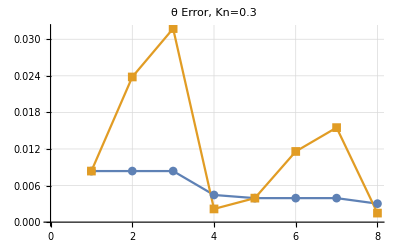

```mathematica
ListPlot[{errorTempKn0p3,errorTempOldKn0p3},Joined->True,GridLines->Automatic,PlotLabel->"θ Error, Kn=0.3",PlotMarkers->Automatic]
```

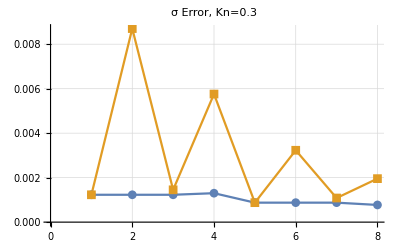

```mathematica
ListPlot[{errorStressKn0p3,errorStressOldKn0p3},Joined->True,GridLines->Automatic,PlotLabel->"σ Error, Kn=0.3",PlotMarkers->Automatic]
```

```mathematica
{errorTempKn0p5,errorStressKn0p5} = {Table[ComputeL2Error[θExactKn0p5,temperatureKn0p5[ii]],{ii,Tensors}],Table[ComputeL2Error[σExactKn0p5,stressKn0p5[ii]],{ii,Tensors}]};
```

```mathematica
{errorTempOldKn0p5,errorStressOldKn0p5} = {Table[ComputeL2Error[θExactKn0p5,temperatureOldKn0p5[ii]],{ii,Tensors}],Table[ComputeL2Error[σExactKn0p5,stressOldKn0p5[ii]],{ii,Tensors}]};
```

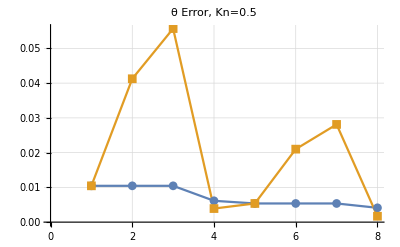

```mathematica
ListPlot[{errorTempKn0p5,errorTempOldKn0p5},Joined->True,GridLines->Automatic,PlotLabel->"θ Error, Kn=0.5",PlotMarkers->Automatic]
```

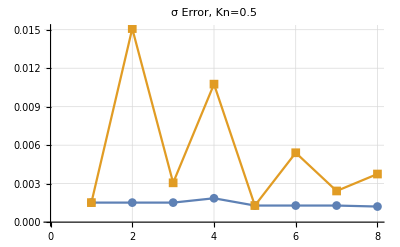

```mathematica
ListPlot[{errorStressKn0p5,errorStressOldKn0p5},Joined->True,GridLines->Automatic,PlotLabel->"σ Error, Kn=0.5",PlotMarkers->Automatic]
```

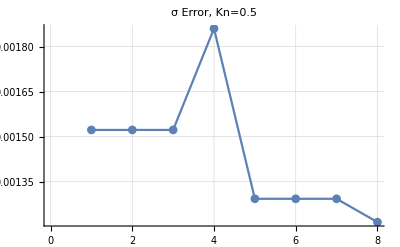

```mathematica
ListPlot[errorStressKn0p5,Joined->True,GridLines->Automatic,PlotLabel->"σ Error, Kn=0.5",PlotMarkers->Automatic]
```

#### error computation (Converge Entropy)

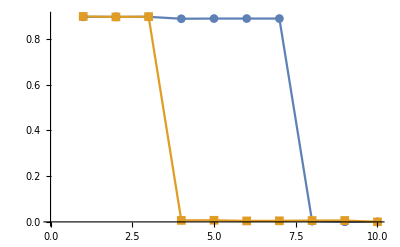

```mathematica
errorEntropyKn0p1 = Quiet[Table[ComputeErrorEntropy[solKn0p1[Tensors⟦-1⟧][x],solKn0p1[ii][x]],{ii,Tensors}]];

errorEntropyOldKn0p1 = Quiet[Table[ComputeErrorEntropy[solOldKn0p1[Tensors⟦-1⟧][x],solOldKn0p1[ii][x]],{ii,Tensors}]];

ListPlot[{errorEntropyKn0p1,errorEntropyOldKn0p1},Joined->True,PlotMarkers->Automatic]
```

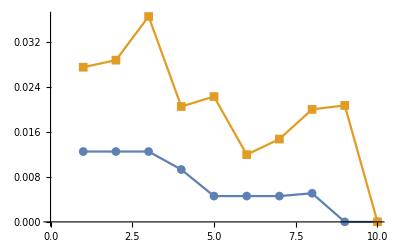

```mathematica
errorEntropyKn0p3 = Quiet[Table[ComputeErrorEntropy[solKn0p3[Tensors⟦-1⟧][x],solKn0p3[ii][x]],{ii,Tensors}]];

errorEntropyOldKn0p3 = Quiet[Table[ComputeErrorEntropy[solOldKn0p3[Tensors⟦-1⟧][x],solOldKn0p3[ii][x]],{ii,Tensors}]];
ListPlot[{errorEntropyKn0p3,errorEntropyOldKn0p3},Joined->True,PlotMarkers->Automatic]
```

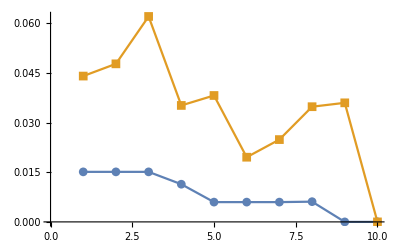

```mathematica
errorEntropyKn0p5 = Quiet[Table[ComputeErrorEntropy[solKn0p5[Tensors⟦-1⟧][x],solKn0p5[ii][x]],{ii,Tensors}]];

errorEntropyOldKn0p5 = Quiet[Table[ComputeErrorEntropy[solOldKn0p5[Tensors⟦-1⟧][x],solOldKn0p5[ii][x]],{ii,Tensors}]];
ListPlot[{errorEntropyKn0p5,errorEntropyOldKn0p5},Joined->True,PlotMarkers->Automatic]
```

# Results (Heat Conduction)

### Sequence of convergence

#### Kn 0.1

```mathematica
Kn = 0.1;
θW=1.0;
α=0;

problemType = 1;
systemType = 1;

Do[Print[Style["Num Tensors: ",FontColor->Magenta],ii];
solHCKn0p1[ii][x_]=GetHeatConduction[Kn,θW,α,ii,systemType,problemType];,{ii,Tensors}];

systemType = 0;
Do[Print[Style["Num Tensors: ",FontColor->Magenta],ii];
solOldHCKn0p1[ii][x_]=GetHeatConduction[Kn,θW,α,ii,systemType,problemType];,{ii,Tensors}];
```

Num Tensors: 6

Num Tensors: 8

Num Tensors: 9

Num Tensors: 11

Num Tensors: 12

Num Tensors: 15

Num Tensors: 16

Num Tensors: 19

Num Tensors: 20

Num Tensors: 24

Num Tensors: 6

Num Tensors: 8

Num Tensors: 9

Num Tensors: 11

Num Tensors: 12

Num Tensors: 15

Num Tensors: 16

Num Tensors: 19

Num Tensors: 20

Num Tensors: 24

#### Kn 0.3

```mathematica
Kn = 0.3;
θW=1.0;
α=0;

problemType = 1;
systemType = 1;

Do[Print[Style["Num Tensors: ",FontColor->Magenta],ii];
solHCKn0p3[ii][x_]=GetHeatConduction[Kn,θW,α,ii,systemType,problemType];,{ii,Tensors}];

systemType = 0;
Do[Print[Style["Num Tensors: ",FontColor->Magenta],ii];
solOldHCKn0p3[ii][x_]=GetHeatConduction[Kn,θW,α,ii,systemType,problemType];,{ii,Tensors}];
```

Num Tensors: 6

Num Tensors: 8

Num Tensors: 9

Num Tensors: 11

Num Tensors: 12

Num Tensors: 15

Num Tensors: 16

Num Tensors: 19

Num Tensors: 20

Num Tensors: 24

Num Tensors: 6

Num Tensors: 8

Num Tensors: 9

Num Tensors: 11

Num Tensors: 12

Num Tensors: 15

Num Tensors: 16

Num Tensors: 19

Num Tensors: 20

Num Tensors: 24

#### error computation (Converge Entropy)

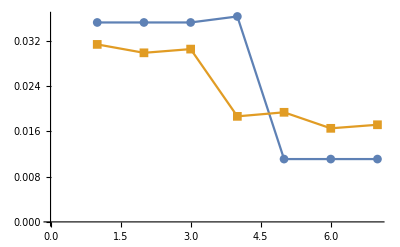

```mathematica
errorEntropyHCKn0p1 = Quiet[Table[ComputeErrorEntropy[solHCKn0p1[Tensors⟦-1⟧][x],solHCKn0p1[ii][x]],{ii,Tensors⟦1;;-4⟧}]];

errorEntropyOldHCKn0p1 = Quiet[Table[ComputeErrorEntropy[solOldHCKn0p1[Tensors⟦-1⟧][x],solOldHCKn0p1[ii][x]],{ii,Tensors⟦1;;-4⟧}]];

ListPlot[{errorEntropyHCKn0p1,errorEntropyOldHCKn0p1},Joined->True,PlotMarkers->Automatic]
```

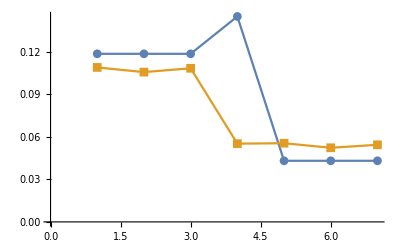

```mathematica
errorEntropyHCKn0p3 = Quiet[Table[ComputeErrorEntropy[solHCKn0p3[Tensors⟦-1⟧][x],solHCKn0p3[ii][x]],{ii,Tensors⟦1;;-4⟧}]];

errorEntropyOldHCKn0p3 = Quiet[Table[ComputeErrorEntropy[solOldHCKn0p3[Tensors⟦-1⟧][x],solOldHCKn0p3[ii][x]],{ii,Tensors⟦1;;-4⟧}]];

ListPlot[{errorEntropyHCKn0p3,errorEntropyOldHCKn0p3},Joined->True,PlotMarkers->Automatic]
```